### Initialization of global variables and importing important structures

```mathematica
(* SET HERE THE WORKING DIRECTORY *)
SetDirectory["C:\\Users\\heikkie13\\Work\\howard_scratches\\Mathematica"];
<<libs/FunctionsComplexAnalysis.m;
<<libs/FunctionsMatrixAnalysis.m;
<<libs/FunctionsFiniteGroups.m;
<<libs/FunctionsGF2.m
<<libs/FunctionsForExtraSpeciality.m;

(* This is needed for the unitary reps of symplectivc matrices: *)
(* <<"SymplecticBinary.m"; *)

(*Clear[AllBinMats];*)
dB = 10*Log[10,N[#]]&;
Clear[mm,rr];
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

```mathematica
(* These are needed for functions to work properly *)
(* The dimension for the simulation must be chosen here, as multiple data structures neede by decoders etc depend on m*)
mm = 3; Nn= 2^mm; InxBin= Tuples[{0,1},{mm}]; WHn = WHmatrix[Nn]/Sqrt[Nn];  InitializeVeryBare[mm];
ZeroVecm = Table[0,{mm}];
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

### Codebook

```mathematica
GenerateChirp = Module[{Sint, bvec,xvec},Sint = #1; bvec = #2;
(xvec  = IntegerDigits[#-1,2,mm];
I^(xvec.Sint.xvec + 2 bvec.xvec)/Sqrt[2^mm]) &/@ Range[2^mm]
]&;

MakeUnitaryFromSymmetric = Module[{Sint,cvec,dvec,Ord2},Sint = #;
 (cvec = IntegerDigits[#-1,2,mm];
Ord2 = cvec.Sint.cvec;
(dvec  = IntegerDigits[#-1,2,mm];
I^(Ord2 + 2 dvec.cvec)/Sqrt[2^mm]
) &/@ Range[2^mm]
) &/@ Range[2^mm] ]&; 

AllBinSymm = GenerateSn2[mm];
AllUmats = MakeUnitaryFromSymmetric[#] &/@ AllBinSymm;
AllUmats // mfl;
CB  = Transpose[Sequence@@(Transpose[#]) &/@ AllUmats]; card = Length[CB[[1]]]; {Length[AllUmats],card}
```

{64,512}

### Decoders

#### Extended decoder

```mathematica
ExtendedDecoder=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest},vecin=#;
squared=vecin*vecin;
squared=squared/Norm[squared];
{Sest, zleft, best, metric}=BreadthFirstDecoding[{squared, Range[mm], 1, False}];
MaskS=Sest/2;
MaskChirp= GenerateChirp[MaskS,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, zleft, best, metric}=BreadthFirstDecoding[{UnmaskedChirp, Range[mm], 1, False}];
{Sest+MaskS,best}]&;
```

#### Truth table calculators and decoding order

```mathematica
DecodingOrder = Module[{vecin, maxis, PermMatEsh, abses, permutetable}, vecin = #;
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
Reverse[Ordering[maxis]]
]&;

GiveTruthTable = Module[{index, size, basetable, binary}, input=#;
index = #1;
size = #2;
binary = Mod[Floor[(Range[2^size] - 1) / 2^(size -index)], 2];
Table[binary[[i]] == 0, {i, 1, 2^size}]
]&;

UpdateTruthTable = Module[{Tt,Tt2, R},
Tt = #1;
R = #2;
Tt2 = GiveTruthTable[R, mm];
Table[Tt[[i]] && Tt2[[i]], {i, 1, Length[Tt]}]
]&;
```

#### Row decoders

```mathematica
DecodeRowList = Module[{start, PauliMat, Metrics, Results, Projectedvectors, Peaks, Peaki, Peakinxs, Sestk, Metrick, Signbitsall, projectedvectors, Sests, Sest, R, K, RangeNow, Tt, vecrot, NewK,  Signbits, Svec, Signbitsk, Sigmak, veck, Mu, WithProjections, avec, bvec, PhaseVec, PermMatEsh, Wht, vecin, Abses, Signs},
Sest = #1;
Signbits = #2;
vecin = #3;
Mu = #4;
Tt = #5;
WithProjections = #6;
K = #7;
R = #8;
start = Transpose[Sest][[R]];
RangeNow=Pick[Range[2^mm],Tt] + FromDigits[start,2];
(* In the end K might be greater than the number of possible different rows *)
NewK = Min[K, Length[RangeNow]];
(* This normalizes out the phase i^{e_i.S.e_i^T} *)
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
PermMatEsh =  PermMatEShifts[[R]];
Wht =  Sqrt[Nn]PhaseVec*DiscreteHadamardTransform[Conjugate[vecin]*(PermMatEsh.vecin), Method->"BitComplement"] // Chop;
Abses = Abs[Wht];
Signs = Sign[Wht];
Metrics = {};
Signbitsall = {};
Projectedvectors = {};
Sests = {};
Peakinxs = Take[Select[Reverse[Ordering[Abses]], MemberQ[RangeNow, #]&], NewK];
Results = (
Peaki = #;
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;
If[WithProjections, Metrick = (Mu + Abses[[Peaki]]) / 2;, Metrick = (Mu + Abses[[Peaki]]);];
Sigmak = Signs[[Peaki]];
Signbitsk = Signbits; 
Signbitsk[[R]] =(1 - Sigmak) / 2;
Svec  = IntegerDigits[Peaki-1,2,mm];
Sestk[[R]]=Svec;
If[WithProjections, avec = ZeroVecm; avec[[R]]=1;
PauliMat = MakePauli[avec,Svec];
vecrot = vecin.PauliMat;
veck = (vecin + Sigmak * vecrot) / 2;
, 
(* This runs if withProjections = False *)
veck = vecin;
];
{Sestk, Signbitsk,veck, Metrick}
)&/@ Peakinxs;
Results
]&;
```

#### List decoder

```mathematica
BreadthFirstDecoding = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowList @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];

If[WithProjections, posi = 1, inners = (best = #[[2]]; (*best = 1 - best;*) Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[vecin].vecest]
) &/@ Candidatelist;
posi = Position[inners,Max[inners]][[1,1]]; ];
Candidatelist[[1]]
]&;
```

### Simulation

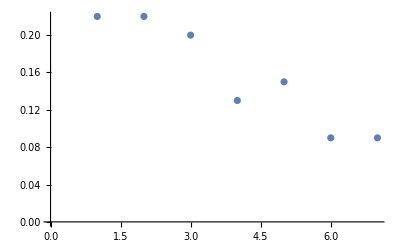

```mathematica
drops = 100;
Ktable = {1,2,3,4,5,20,512};
Errortable ={};
(K = #;
errors = 0;
(
(*tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];*)
tstvec = E^(I*2Pi*RandomReal[10, 8]); tstvec = tstvec/Norm[tstvec];
inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ClosestVec = Transpose[CB][[posi]];

{Sest, best, zleft, metric} = BreadthFirstDecoding[tstvec, K,False, Range[mm]];Sest //mf;
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Dist2 = 1-Abs[ClosestVec.Conjugate[vecest]]^2 ;
If[Abs[ClosestVec.Conj[vecest]]<= 0.99,errors = errors+1];
)&/@ Range[drops];
AppendTo[Errortable, errors];
)&/@Ktable;
ListPlot[Errortable/drops]
```

```mathematica
(* COMMUNICATION SCENARIO SIMULATION 
Timing[
drops = 1125*100;
SNRValues = Range[-10,15,1];
ResultsNew = {};
ResultsOld = {};
(SNR = #;
gamma = 10^(SNR/10);
errors = 0;
(
Smatrix = RandomChoice[ExtendedSmats];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate,bestimate}=ExtendedDecoder[tstvec];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors += 1];
)&/@ Range[drops];
AppendTo[ResultsNew, {SNR, errors/drops//N}];
errors = 0;
(
Smatrix = RandomChoice[AllBinSymm];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate, zleft, bestimate, metric}=BreadthFirstDecoding[{tstvec, Range[mm], 1, False}];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors += 1];
)&/@ Range[drops];
AppendTo[ResultsOld, {SNR, errors/drops//N}];
)&/@ SNRValues;]
Print[ResultsNew];
Print[ResultsOld];
ListLinePlot[{ResultsNew, ResultsOld}, PlotLegends->{"Extended codebook", "Binary chirp codebook"}] *)
```

```mathematica
noise = E^(I*2Pi*RandomReal[10, 8])
Conj[noise].MakePauli[RandomChoice[{0,1},3],RandomChoice[{0,1},3]].noise
```

{-0.629861+0.776708 ⅈ,-0.651872+0.758329 ⅈ,0.692965+0.720971 ⅈ,-0.830739-0.556662 ⅈ,-0.926518-0.37625 ⅈ,-0.446253+0.894907 ⅈ,0.983068+0.18324 ⅈ,0.633651-0.773619 ⅈ}

0.0508489+1.11022×10^-16 ⅈ

```mathematica
R = 2;
vecin = E^(I*2Pi*RandomReal[10, 8]);
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
PermMatEsh =  PermMatEShifts[[R]];
Wht =  Sqrt[Nn]PhaseVec*DiscreteHadamardTransform[Conjugate[vecin]*(PermMatEsh.vecin), Method->"BitComplement"]
```

{-1.42592+0. ⅈ,4.72054+0. ⅈ,-1.54855+0. ⅈ,0.463559+0. ⅈ,0.394979+0. ⅈ,1.85995+0. ⅈ,5.66112+0. ⅈ,1.18604+0. ⅈ}

```mathematica
Sqrt[Nn]PhaseVec*vecin.MakePauli[avec, {0,1,1}].vecin
```

{3.14018×10^-16+6.28037×10^-16 ⅈ,3.14018×10^-16+6.28037×10^-16 ⅈ,6.28037×10^-16-3.14018×10^-16 ⅈ,6.28037×10^-16-3.14018×10^-16 ⅈ,3.14018×10^-16+6.28037×10^-16 ⅈ,3.14018×10^-16+6.28037×10^-16 ⅈ,6.28037×10^-16-3.14018×10^-16 ⅈ,6.28037×10^-16-3.14018×10^-16 ⅈ}

```mathematica
RandomChoice[{0,1},3]
```

{1,1,1}

```mathematica
MakePauli[{0,0,0},{0,1,0}]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}

```mathematica
Conj[noise].MakePauli[{0,0,0},{1,0,1}].noise
```

1.11022×10^-16+0. ⅈ